Electric Field

28200000/543169

The central frequency is 407.056 THz

The frequency bandwidth is 51.9175 THz

-Graphics-

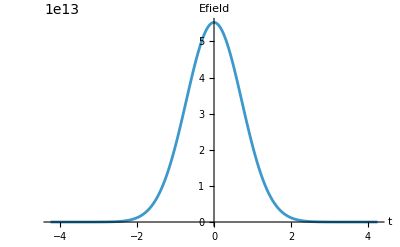

```mathematica
(* parameters*)
ClearAll["Global`*"]

λ = 737*10^(-9); (*m*)
fo = (3*10^(8)/λ)*10^(-12); (*THz*)
ωo = 2*Pi*fo*10^(12); (*rad/s*)
Δλ = 94*10^(-9);  (*m*)
Δf= ((3*10^8)/λ^2*Δλ)*10^(-12) (*Thz*)
Δω = 2*Pi*Δf*10^(12);
Δt = .441/(Δf*10^(12)); (*s*)

A = 1;

tmin=-5*Δt;
tmax=5*Δt;
tmin1=-5*Δt;
tmax1=5*Δt;
ωmin = -5*Δω+ωo;
ωmax = 5*Δω+ωo;

σt = Δt/(2*√(2*Log[2]));
σω = Δω/(2*√(2*Log[2]));

Print["The central frequency is ", N[fo], " THz"]
Print["The frequency bandwidth is ", N[Δf], " THz"]

(* E field in the frequency domain*)
Efieldω[ω_] := A* Exp[-(ω-ωo)^2/(2σω^2)];

(*E field in the time domain Fourier transformed from the frequency domain*)
Efieldt[t_] =∫_(-∞)^∞ (1/(2Pi))Efieldω[w]Exp[-I*w*t]ⅆw;

Plot[Efieldω[ω],{ω,ωmin,ωmax},PlotPoints->500,MaxRecursion->4,PlotRange->All, AxesLabel->{ω, Efield}]
Plot[Abs[Efieldt[t]], {t, tmin1, tmax1}, PlotPoints->500, MaxRecursion->4, PlotRange->All, AxesLabel->{t, Efield}]
```

Sellemeier Equations

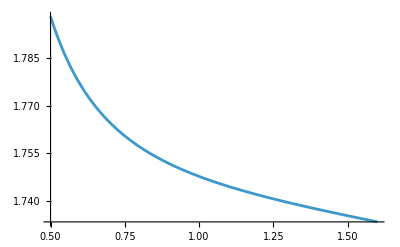

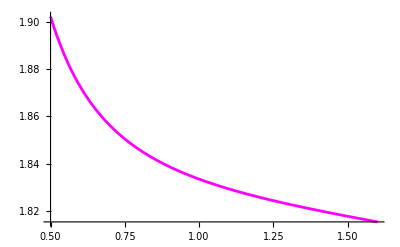

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Sellemeier Equations for PPKTP*)
(*z axis: https://doi.org/10.1063/1.123408*)(*y axis: https://doi.org/10.1063/1.1668320*)
(*temperature dependence: https://opg.optica.org/ao/fulltext.cfm?uri=ao-42-33-6661*)

(*y*)
A1y = 2.09930;
A2y = 0.922683;
A3y = 0.0467695;
A4y = 0.0138408;

(*z*)
Az = 2.12725;
Bz = 1.18431;
Cz = 5.14852*10^-2;
Dz = 0.6603;
Ez = 100.00507;
Fz = 9.68956*10^-3;

temp = 60;

n1z[λ_] := 9.9587*10^-6 + 9.9228*10^-6/λ + -8.9603*10^-6/(λ^2) + 4.1010*10^-6/(λ^3);
n2z[λ_] := -1.1882*10^-8 + 10.459*10^-8/λ + -9.8136*10^-8/(λ^2) + 3.1481*10^-8/(λ^3);
Δnz[λ_] := n1z[λ]*(temp - 25) + n2z[λ]*(temp - 25)^2;

n1y[λ_] := 6.2897*10^-6 + 6.3061*10^-6/λ + -6.0629*10^-6/(λ^2) + 2.6486*10^-6/(λ^3);
n2y[λ_] := -.14445*10^-8 + 2.2244*10^-8/λ + -3.5770*10^-8/(λ^2) + 1.3470*10^-8/(λ^3);
Δny[λ_] := n1y[λ]*(temp - 25) + n2y[λ]*(temp - 25)^2;

ny[λ_] := Sqrt[A1y + A2y/(1 - A3y/(λ^2)) - A4y*λ^2] + Δny[λ];

nz[λ_] := Sqrt[Az + Bz/(1 - Cz/(λ^2)) + Dz/(1 - Ez/(λ^2)) - Fz*λ^2] + Δnz[λ];

p1 = Plot[ny[λ], {λ, 0.5, 1.6}]
p2 = Plot[nz[λ], {λ, 0.5, 1.6}, PlotStyle -> Magenta]
```

Poling Period

```mathematica
λpo = 520*10^-9; 
λso = 780*10^-9; 
λio = 1/(1/λpo -1/λso);
c = 3*10^8;

Print["The central wavelength for the idler is ", N[λio], "m"]

ωpo = 2π c/λpo;
ωso = 2π c/λso;
ωio = 2π c/λio;

kpo = nz[λpo*10^6]*ωpo/c;
kso = nz[λso*10^6]*ωso/c;
kio = nz[λio*10^6]*ωio/c;

Λ = (-2π/(-kpo + kso +kio))*10^6;
Print["The poling period is ", N[Λ], " microns"]
```

The central wavelength for the idler is 1.56×10^-6m

The poling period is 9.05838 microns

JSI (no cavity)

```mathematica
Clear[λi, λs];

Δt=1*10^-9;
Δν=(.441/Δt) /10^9;
σν=Δν/(2*Sqrt[2*Log[2]]);

λs[ν_]:=c/ν;
λi[ν_]:=c/ν;

L = 1*10^-2;

νso = (c/λso) /10^9;
νio = (c/λio) /10^9;
νpo = (c/λpo) /10^9;

Print["The central frequency for the signal is ", N[νso], " Ghz"];
Print["The central frequency for the idler is ", N[νio], " Ghz"];


Δk0 = -nz[λpo*10^6]*2π *νpo*10^9/c + nz[λso*10^6]*2π *νso*10^9/c + nz[λio*10^6]*2π * νio*10^9/c  + 2π/(Λ*10^-6) ;
Print["Delta k0 is ",N[Δk0]]

 (*next order term*)
dkp = D[2π nz[(c/(νp*10^9))*10^6] (νp*10^9/c), νp] /. νp -> νpo;
dks = D[2π nz[(c/(νs*10^9))*10^6] (νs*10^9/c), νs] /. νs -> νso;
dki = D[2π nz[(c/(νi*10^9))*10^6] (νi*10^9/c), νi] /. νi -> νio;
Δk1[ Δνs_,Δνi_]:=(dkp-dks)*Δνs+(dkp-dki)*Δνi;

Δk[ Δνs_,Δνi_]:= Δk0  + Δk1[ Δνs,Δνi]  ;
α[Δνs_,Δνi_] := A* Exp[-(Δνs + Δνi)^2/(2σν^2)];
ϕ[Δνs_, Δνi_] := Sinc[(Δk[Δνs,Δνi] *L)/2];

JSA[Δνs_,Δνi_] := ϕ[Δνs,Δνi]*α[Δνs, Δνi];
JSI[Δνs_, Δνi_] := JSA[Δνs,Δνi]*Conjugate[JSA[Δνs,Δνi]];

δν = 7;

DensityPlot[α[Δνs,Δνi],{Δνs,-δν,δν},{Δνi,-δν,δν}, PlotPoints->100, PlotRange->All, PlotLabel->"Pump (Detuning)",FrameLabel->{"Signal (GHz)","idler (Ghz)",None,None}]
DensityPlot[ϕ[Δνs,Δνi],{Δνs,-δν,δν},{Δνi,-δν,δν}, PlotPoints->100, PlotRange->All, PlotLabel->"Phasematching (Detuning)",FrameLabel->{"Signal (GHz)","idler (Ghz)",None,None}]
DensityPlot[JSI[Δνs,Δνi],{Δνs,-δν,δν},{Δνi,-δν,δν},PlotPoints->100, PlotRange->All, PlotLabel->"JSI (Detuning)",FrameLabel->{"Signal (GHz)","idler (Ghz)",None,None}]
```

The central frequency for the signal is 384615. Ghz

The central frequency for the idler is 192308. Ghz

Delta k0 is 0.

General::munfl: Exp[-2794.13] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

-Graphics-

General::munfl: Exp[-2794.13] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

Cavity Physics

The finesse is 1686.04

The spectral width is: 0.0048154 Ghz

The spectral width with no loss is: 0.00259015 Ghz

The free spectral range is 8.11893 GHz

0.3

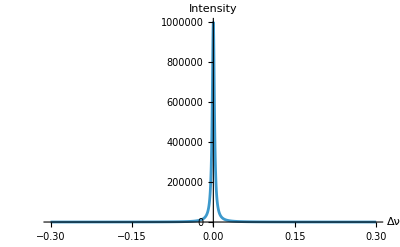

```mathematica
L = 1*10^-2;
(*Reflectivity*)
R1 = .999499;
R2 = .999499;
R=Sqrt[R1*R2];
(*loss coefficient for absorption for PPKTP at 775 (ppm/cm)*)
αs = 127*10^-6*100;
(*αr = αs+ 1/(2*L)Log[1/(R1*R2)];*)
αr = .18633;

(*Finesse*)
Fnoloss = (π √(R1*R2))/(1-R1*R2);
F = (π*Exp[-αr*L/2])/(1 - Exp[-αr*L]);
Print["The finesse is ", N[F]];
(*Free spectral range*)
νf = (c*10^-9)/(2*L*nz[λso*10^6]);
(*Spectral width*)
sw = νf/F;
swnoloss = νf/Fnoloss;
Print["The spectral width is: ", N[sw], " Ghz"]
Print["The spectral width with no loss is: ", N[swnoloss], " Ghz"]
(*Internal resonator intensity*)
Io = 1;

Imax = Io/(1-R1*R2)^2;
Print["The free spectral range is ",νf, " GHz"]

Intensity[ Δν_]:= Imax/(1 + ((2*F)/π)^2*(Sin[(π*Δν)/νf])^2);
δν2 = .3

Plot[Intensity[Δν],{Δν,-δν2,δν2},PlotPoints->100,PlotRange->All, AxesLabel->{Δν, Intensity}]
```

JSI (cavity)

```mathematica
JSA[Δνs_,Δνi_] := ϕ[Δνs,Δνi]*α[Δνs, Δνi]*Intensity[Δνs];
JSI[Δνs_, Δνi_] := JSA[Δνs,Δνi]*Conjugate[JSA[Δνs,Δνi]];
DensityPlot[JSI[Δνs,Δνi],{Δνs,-δν2,δν2},{Δνi,-δν2,δν2},PlotPoints->100, PlotRange->All, PlotLabel->"JSI",FrameLabel->{"Signal (GHz)","idler (Ghz)",None,None}]
```

-Graphics-